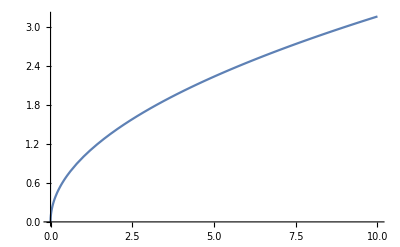

```mathematica
Plot[√x,{x,0,10}]
```

```mathematica
Integrate[1-√x,{x,0,Infinity}]
```

Integrate::idiv: Integral of 1 - √x does not converge on {0, ∞}.

∫_0^∞ (1-√x)ⅆx

```mathematica
Solve[x*(1+b*(1-(√x)))-r== 0,x]
```

{{x→-(-1-2 b-b^2)/(3 b^2)-(2^(1/3) (-(-1-2 b-b^2)^2+6 b^2 (1+b) r))/(3 b^2 (2+12 b+30 b^2+40 b^3+30 b^4+12 b^5+2 b^6-18 b^2 r-54 b^3 r-54 b^4 r-18 b^5 r+27 b^4 r^2+√(-108 b^6 r^3-324 b^7 r^3-324 b^8 r^3-108 b^9 r^3+729 b^8 r^4))^(1/3))+((2+12 b+30 b^2+40 b^3+30 b^4+12 b^5+2 b^6-18 b^2 r-54 b^3 r-54 b^4 r-18 b^5 r+27 b^4 r^2+√(-108 b^6 r^3-324 b^7 r^3-324 b^8 r^3-108 b^9 r^3+729 b^8 r^4))^(1/3))/(3 2^(1/3) b^2)},{x→-(-1-2 b-b^2)/(3 b^2)+((1+ⅈ √3) (-(-1-2 b-b^2)^2+6 b^2 (1+b) r))/(3 2^(2/3) b^2 (2+12 b+30 b^2+40 b^3+30 b^4+12 b^5+2 b^6-18 b^2 r-54 b^3 r-54 b^4 r-18 b^5 r+27 b^4 r^2+√(-108 b^6 r^3-324 b^7 r^3-324 b^8 r^3-108 b^9 r^3+729 b^8 r^4))^(1/3))-((1-ⅈ √3) (2+12 b+30 b^2+40 b^3+30 b^4+12 b^5+2 b^6-18 b^2 r-54 b^3 r-54 b^4 r-18 b^5 r+27 b^4 r^2+√(-108 b^6 r^3-324 b^7 r^3-324 b^8 r^3-108 b^9 r^3+729 b^8 r^4))^(1/3))/(6 2^(1/3) b^2)},{x→-(-1-2 b-b^2)/(3 b^2)+((1-ⅈ √3) (-(-1-2 b-b^2)^2+6 b^2 (1+b) r))/(3 2^(2/3) b^2 (2+12 b+30 b^2+40 b^3+30 b^4+12 b^5+2 b^6-18 b^2 r-54 b^3 r-54 b^4 r-18 b^5 r+27 b^4 r^2+√(-108 b^6 r^3-324 b^7 r^3-324 b^8 r^3-108 b^9 r^3+729 b^8 r^4))^(1/3))-((1+ⅈ √3) (2+12 b+30 b^2+40 b^3+30 b^4+12 b^5+2 b^6-18 b^2 r-54 b^3 r-54 b^4 r-18 b^5 r+27 b^4 r^2+√(-108 b^6 r^3-324 b^7 r^3-324 b^8 r^3-108 b^9 r^3+729 b^8 r^4))^(1/3))/(6 2^(1/3) b^2)}}

```mathematica
Plot3D[-(-1-2 b-b^2)/(3 b^2)-(2^(1/3) (-(-1-2 b-b^2)^2+6 b^2 (1+b) r))/(3 b^2 (2+12 b+30 b^2+40 b^3+30 b^4+12 b^5+2 b^6-18 b^2 r-54 b^3 r-54 b^4 r-18 b^5 r+27 b^4 r^2+√(-108 b^6 r^3-324 b^7 r^3-324 b^8 r^3-108 b^9 r^3+729 b^8 r^4))^(1/3))+((2+12 b+30 b^2+40 b^3+30 b^4+12 b^5+2 b^6-18 b^2 r-54 b^3 r-54 b^4 r-18 b^5 r+27 b^4 r^2+√(-108 b^6 r^3-324 b^7 r^3-324 b^8 r^3-108 b^9 r^3+729 b^8 r^4))^(1/3))/(3 2^(1/3) b^2),{b,0,2},{r,1,2},PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
f=1-√(-(-1-2 b-b^2)/(3 b^2)-(2^(1/3) (-(-1-2 b-b^2)^2+6 b^2 (1+b) r))/(3 b^2 (2+12 b+30 b^2+40 b^3+30 b^4+12 b^5+2 b^6-18 b^2 r-54 b^3 r-54 b^4 r-18 b^5 r+27 b^4 r^2+√(-108 b^6 r^3-324 b^7 r^3-324 b^8 r^3-108 b^9 r^3+729 b^8 r^4))^(1/3))+((2+12 b+30 b^2+40 b^3+30 b^4+12 b^5+2 b^6-18 b^2 r-54 b^3 r-54 b^4 r-18 b^5 r+27 b^4 r^2+√(-108 b^6 r^3-324 b^7 r^3-324 b^8 r^3-108 b^9 r^3+729 b^8 r^4))^(1/3))/(3 2^(1/3) b^2))
```

```mathematica
Plot3D[1-√(-(-1-2 b-b^2)/(3 b^2)-(2^(1/3) (-(-1-2 b-b^2)^2+6 b^2 (1+b) r))/(3 b^2 (2+12 b+30 b^2+40 b^3+30 b^4+12 b^5+2 b^6-18 b^2 r-54 b^3 r-54 b^4 r-18 b^5 r+27 b^4 r^2+√(-108 b^6 r^3-324 b^7 r^3-324 b^8 r^3-108 b^9 r^3+729 b^8 r^4))^(1/3))+((2+12 b+30 b^2+40 b^3+30 b^4+12 b^5+2 b^6-18 b^2 r-54 b^3 r-54 b^4 r-18 b^5 r+27 b^4 r^2+√(-108 b^6 r^3-324 b^7 r^3-324 b^8 r^3-108 b^9 r^3+729 b^8 r^4))^(1/3))/(3 2^(1/3) b^2)),{r,0,2},{b,0,2.5}]
```

-Graphics3D-

```mathematica
Solve[x*(1+a*b*f)-p+k== x*(1+b*f)-r,x]
```

{{x→(-k+p-r)/((-1+a) b f)}}

```mathematica
Solve [D[p*(1-√((-k+p-r)/((-1+a) b f))),p]==0,p]
```

{{p→2/9 (-b f+a b f+3 k+3 r-√(b^2 f^2-2 a b^2 f^2+a^2 b^2 f^2+3 b f k-3 a b f k+3 b f r-3 a b f r))},{p→2/9 (-b f+a b f+3 k+3 r+√(b^2 f^2-2 a b^2 f^2+a^2 b^2 f^2+3 b f k-3 a b f k+3 b f r-3 a b f r))}}

```mathematica
2/9 (-b f+a b f+3 k+3 r-√(b^2 f^2-2 a b^2 f^2+a^2 b^2 f^2+3 b f k-3 a b f k+3 b f r-3 a b f r))
```

2/9 (-b f+a b f+3 k+3 r-√(b^2 f^2-2 a b^2 f^2+a^2 b^2 f^2+3 b f k-3 a b f k+3 b f r-3 a b f r))

```mathematica
Manipulate[Plot[{2/9 (-b f+a b f+3 k+3 r-√(b^2 f^2-2 a b^2 f^2+a^2 b^2 f^2+3 b f k-3 a b f k+3 b f r-3 a b f r)),2/9 (-b f+a b f+3 k+3 r+√(b^2 f^2-2 a b^2 f^2+a^2 b^2 f^2+3 b f k-3 a b f k+3 b f r-3 a b f r))},{r,0,2}],{a,0,3},{b,0,2},{f,0,1},{k,0,2}]
```

```mathematica
Solve [{D[p*(1-√((-k+p-r)/((-1+a) b f)))-k^2,k]==0,D[p*(1-√((-k+p-r)/((-1+a) b f)))-k^2,p]==0},{p,k}]
```

{{p→1/3 (-2 b f+2 a b f-1/(12 (-b f+a b f))-(5 b f)/(6 (-b f+a b f))+(5 a b f)/(6 (-b f+a b f))-(4 b^2 f^2)/(3 (-b f+a b f))+(8 a b^2 f^2)/(3 (-b f+a b f))-(4 a^2 b^2 f^2)/(3 (-b f+a b f))+2 r+(√((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(12 (-b f+a b f))+(b f √((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(6 (-b f+a b f))-(a b f √((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(6 (-b f+a b f))),k→(-1-8 b f+8 a b f+√((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(24 (-b f+a b f))},{p→1/3 (-2 b f+2 a b f-1/(12 (-b f+a b f))-(5 b f)/(6 (-b f+a b f))+(5 a b f)/(6 (-b f+a b f))-(4 b^2 f^2)/(3 (-b f+a b f))+(8 a b^2 f^2)/(3 (-b f+a b f))-(4 a^2 b^2 f^2)/(3 (-b f+a b f))+2 r-(√((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(12 (-b f+a b f))-(b f √((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(6 (-b f+a b f))+(a b f √((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(6 (-b f+a b f))),k→(-1-8 b f+8 a b f-√((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(24 (-b f+a b f))}}

```mathematica
Manipulate[Plot3D[{1/3 (-2 b f+2 a b f-1/(12 (-b f+a b f))-(5 b f)/(6 (-b f+a b f))+(5 a b f)/(6 (-b f+a b f))-(4 b^2 f^2)/(3 (-b f+a b f))+(8 a b^2 f^2)/(3 (-b f+a b f))-(4 a^2 b^2 f^2)/(3 (-b f+a b f))+2 r+(√((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(12 (-b f+a b f))+(b f √((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(6 (-b f+a b f))-(a b f √((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(6 (-b f+a b f)))*(1-√(1/((-1+a) b f)(-(-1-8 b f+8 a b f+√((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(24 (-b f+a b f))+1/3 (-2 b f+2 a b f-1/(12 (-b f+a b f))-(5 b f)/(6 (-b f+a b f))+(5 a b f)/(6 (-b f+a b f))-(4 b^2 f^2)/(3 (-b f+a b f))+(8 a b^2 f^2)/(3 (-b f+a b f))-(4 a^2 b^2 f^2)/(3 (-b f+a b f))+2 r+(√((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(12 (-b f+a b f))+(b f √((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(6 (-b f+a b f))-(a b f √((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(6 (-b f+a b f)))-r)))-((-1-8 b f+8 a b f+√((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(24 (-b f+a b f)))^2,1/3 (-2 b f+2 a b f-1/(12 (-b f+a b f))-(5 b f)/(6 (-b f+a b f))+(5 a b f)/(6 (-b f+a b f))-(4 b^2 f^2)/(3 (-b f+a b f))+(8 a b^2 f^2)/(3 (-b f+a b f))-(4 a^2 b^2 f^2)/(3 (-b f+a b f))+2 r-(√((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(12 (-b f+a b f))-(b f √((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(6 (-b f+a b f))+(a b f √((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(6 (-b f+a b f)))*(1-√(1/((-1+a) b f)(-(-1-8 b f+8 a b f-√((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(24 (-b f+a b f))+1/3 (-2 b f+2 a b f-1/(12 (-b f+a b f))-(5 b f)/(6 (-b f+a b f))+(5 a b f)/(6 (-b f+a b f))-(4 b^2 f^2)/(3 (-b f+a b f))+(8 a b^2 f^2)/(3 (-b f+a b f))-(4 a^2 b^2 f^2)/(3 (-b f+a b f))+2 r-(√((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(12 (-b f+a b f))-(b f √((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(6 (-b f+a b f))+(a b f √((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(6 (-b f+a b f)))-r)))-((-1-8 b f+8 a b f-√((1+8 b f-8 a b f)^2-4 (-12 b f+12 a b f) (-b f+a b f+r)))/(24 (-b f+a b f)))^2},{r,0,2},{b,0,2.5}],{a,1,4}]
```